# Setup

## General

```mathematica
Get["DiFfRG`"]
SetDirectory[GetDirectory[]];
DefineFormExecutable["/usr/bin/tform -w16"]
```

Mathematica package DiFfRG loaded
Authors: Franz Richard Sattler
Version: 2.0
Year: 2025

Loading external dependencies...

TensorBases loaded

MaTeX loaded

Loading modules...

...FEDeriK loaded

...AnSEL loaded

...DiANE loaded

...DiRK loaded

...TRACY loaded

...COEN loaded

...SeDecA loaded

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0
Year: 2025
For more information, call FInfo[].

DiFfRG CodeTools: Flow output directory is set to 
        /home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/
This can be modified by using SetFlowName["YourNewName"]

TFORM 4.3.1 (Apr 11 2023, v4.3.1) 64-bits

## Defining the theory

```mathematica
fields= <|
"Commuting"-> {A[p,{v, c}]},
"Grassmann"->{{cb[p,{c}],c[p,{c}]}}
|>;
```

```mathematica
truncation=<|
GammaN->{{A,A},{A,A,A},{A,A,A,A},{A,cb,c},{cb,c}},
Propagator->{{A,A},{cb,c}},Rdot->{{A,A},{cb,c}},
S->{{A,A},{A,A,A},{A,A,A,A},{cb,c},{cb,c,A}},
Field->{{}}
|>;
```

```mathematica
bases=<|
GammaN->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
S->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
Propagator->{{A,A}->{"AA",1},{cb,c}->"cbc"},
Rdot->{{A,A}->{"AA",1},{cb,c}->"cbc"}
|>;
```

```mathematica
diagramStyling=<|
"Styles"->{A->{Orange},c->{Black,Dashed}}
|>;
SetTexStyles[cb->"\\bar{c}"];
```

```mathematica
Setup=<|
"FieldSpace"->fields,
"Truncation"->truncation,
"FeynmanRules"->bases,
"DiagramStyling"->diagramStyling
|>;
SetGlobalSetup[Setup];
```

## Feynman rules

### Momentum configurations

```mathematica
SP3Patt[p1e_,p2e_,p3e_]:={√((sp[p1,p1]+sp[p2,p2]+sp[p3,p3])/3)}/.{p1:>p1e,p2:>p2e,p3:>p3e}//UseLorentzLinearity//FullSimplify;
SP4Patt[p1e_,p2e_,p3e_,p4e_]:={√((sp[p1,p1]+sp[p2,p2]+sp[p3,p3]+sp[p4,p4])/4)}/.{p1:>p1e,p2:>p2e,p3:>p3e,p4:>p4e}//UseLorentzLinearity//FullSimplify;
```

### Rules

```mathematica
dressingRules=ReplaceRepeated[#,{
dressing[GammaN,{cb,c},1,{p1_,p2_}]:>-Zc[√sp[p2,p2]]sp[p2,p2],
dressing[GammaN,{A,A},1,{p1_,p2_}]:>ZA[√sp[p2,p2]]sp[p2,p2],

dressing[InverseProp,{cb,c},1,{p1_,p2_}]:>-(Zc[√sp[p2,p2]]sp[p2,p2]+RB[k^2,sp[p2,p2]]Zc[k]),
dressing[InverseProp,{A,A},1,{p1_,p2_}]:>ZA[√sp[p2,p2]]sp[p2,p2]+RB[k^2,sp[p2,p2]]ZA[evP],

dressing[GammaN,{A,cb,c},1,{p1_,p2_,p3_}]:>ZAcbc[p1,p2], 
dressing[GammaN,{A,A,A},1,{p1_,p2_,p3_}]:>ZA3[p1,p2], 
dressing[GammaN,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>ZA4[p1,p2,p3] ,

ZAcbc[p1_,p2_]:>ZAcbc@@SP3Patt[p1,p2,-p1-p2],
ZA3[p1_,p2_]:>ZA3@@SP3Patt[p1,p2,-p1-p2],
ZA4[p1_,p2_,p3_]:>ZA4@@SP4Patt[p1,p2,p3,-p1-p2-p3],

nZA->6,
evP:>(k^nZA+1)^(1/nZA),
devP:>k^(-1+nZA) (1+k^nZA)^(-1+1/nZA),
dressing[Rdot,{A,A},1,{p1_,p2_}]:>ZA[evP]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZA[evP]+k*devP*(ZA[1.02evP]-ZA[evP])/(0.02*evP)),
dressing[Rdot,{cb,c},1,{p1_,p2_}]:>Zc[k]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZc[k]+k(Zc[1.02*k]-Zc[k])/(0.02*k))
}]&;

SetSymmetricDressing[GammaN,{A,A}]
```

### Parametrizations

```mathematica
PropParam[expr_]:=UseLorentzLinearity[expr]//.{
sp[p1,p1]->p^2,sp[l2,l2]->l2^2,sp[l1,l1]->l1^2,sp[l1,p1]->l1 p cos[p,l1],sp[l2,p1]->l2 p cos[p,l2],sp[l1,l2]->l1 l2 cos[l1,l2],√(a_^2):>a,(a_^2)^(n_/2):>a^n,
cos[l1,p]:>cos1
}//FORMSimplify;

SP3FormRule=MakeSPFormRule[{l1},p,{p1,p2,p3}];
SP4FormRule=MakeSPFormRule[{l1},p,{p1,p2,p3,p4}];
SPParam[expr_]:=UseLorentzLinearity[expr]//.{sp[p,p]->p^2,sp[l1,l1]->l1^2,√(a_^2):>a,(a_^2)^(n_/2):>a^n,(a_^2)^(n_/2):>a^n,Power[Power[l1_,2],Rational[n_,2]]:>l1^n,
cos[l1,p1]:>cosl1p1,
cos[l1,p2]:>cosl1p2,
cos[l1,p3]:>cosl1p3,
cos[l1,p4]:>cosl1p4
}//FORMSimplify;

SetNc[3]
$Assumptions=k>0&&p>0&&l1>0&&-1<cos1<1&&-1<cos2<1&&-1<cos3<1;
```

```mathematica
symmetryP2={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2}]],{i1,i2}};
symmetryP3={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3}]],{i1,i2,i3}};
symmetryP4={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3,4}]],{i1,i2,i3,i4}};
```

## Code Generation

```mathematica
kernelZA=<|"Name"->"ZA","Integrator"->"Integrator_p2_1ang","d"->4,"AD"->False,"Type"->"double","Device"->"GPU"|>;
kernelZc=<|"Name"->"Zc","Integrator"->"Integrator_p2_1ang","d"->4,"AD"->False,"Type"->"double","Device"->"GPU"|>;
kernelZA3=<|"Name"->"ZA3","Integrator"->"Integrator_p2_4D_2ang","d"->4,"AD"->False,"Type"->"double","Device"->"GPU"|>;
kernelZAcbc=<|"Name"->"ZAcbc","Integrator"->"Integrator_p2_4D_2ang","d"->4,"AD"->False,"Type"->"double","Device"->"GPU"|>;
kernelZA4=<|"Name"->"ZA4","Integrator"->"Integrator_p2_4D_3ang","d"->4,"AD"->False,"Type"->"double","Device"->"GPU"|>;

interpolatorType="SplineInterpolator1D<double, LogarithmicCoordinates1D<double>, GPU_memory>";

kernelParameterList={
<|"Name"->"k","Type"->"double"|>,
(*strong couplings*)
<|"Name"->"ZA3","Type"->interpolatorType,"Const"->True,"Reference"->True|>,
<|"Name"->"ZAcbc","Type"->interpolatorType,"Const"->True,"Reference"->True|>,
<|"Name"->"ZA4","Type"->interpolatorType,"Const"->True,"Reference"->True|>,
(*ghost propagator*)
<|"Name"->"dtZc","Type"->interpolatorType,"Const"->True,"Reference"->True|>,
<|"Name"->"Zc","Type"->interpolatorType,"Const"->True,"Reference"->True|>,
(*glue propagator*)
<|"Name"->"dtZA","Type"->interpolatorType,"Const"->True,"Reference"->True|>,
<|"Name"->"ZA","Type"->interpolatorType,"Const"->True,"Reference"->True|>
};
```

```mathematica
SP4Defs=DeclareSymmetricPoints4DP4[l1,p,{p1,p2,p3,p4}];
SP3Defs=DeclareSymmetricPoints4DP3[l1,p,{p1,p2,p3}];
```

# Flows

## Propagators

## Gluon propagator


--Graphics-/2--Graphics---Graphics-+-Graphics-

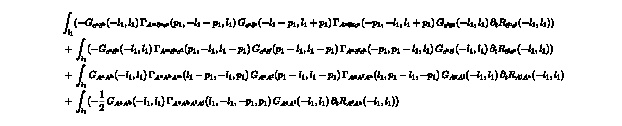

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA/ZA.hh unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA/kernel.hh unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA/src/constructor.cc unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA/src/CT_get.cc unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA/src/CT_map_1.cc unchanged

Please run UpdateFlows[] to export an up-to-date CMakeLists.txt

Exported to "/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/CMakeLists.txt"

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.hh unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.cc unchanged

```mathematica
fRGAA=TakeDerivatives[WetterichEquation,{A[i1],A[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;

traceExprAA=F[TBGetProjector["AA",1,{i1,i2}/.fRGAA["1-Loop"]["ExternalIndices"]],(fRGAA["1-Loop"]["Expression"]/.MakeDiagrammaticRules[])];
FlowAA=FormTrace[traceExprAA]//dressingRules//FORMSimplify//PropParam;

MakeKernel[FlowAA/p^2,kernelZA,kernelParameterList,
"IntegrationVariables"->{"l1","cos1"},
"Coordinates"->{"LogarithmicCoordinates1D<double>"},
"CoordinateArguments"->{"p"}]
UpdateFlows["YangMillsFlows"]
```

## Ghost propagator

```mathematica
fRGcbc=TakeDerivatives[WetterichEquation,{cb[i1],c[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;

traceExprcbc=F[TBGetProjector["cbc",1,{i1,i2}/.fRGcbc["1-Loop"]["ExternalIndices"]],(fRGcbc["1-Loop"]["Expression"]/.MakeDiagrammaticRules[])];
Flowcbc=FormTrace[traceExprcbc]//dressingRules//FORMSimplify//PropParam;

MakeKernel[-Flowcbc/p^2//Expand//Simplify,kernelZc,kernelParameterList,
"IntegrationVariables"->{"l1","cos1"},
"Coordinates"->{"LogarithmicCoordinates1D<double>"},
"CoordinateArguments"->{"p"}]
UpdateFlows["YangMillsFlows"]
```

--Graphics---Graphics-

-Graphics-

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/Zc/Zc.hh unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/Zc/kernel.hh unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/Zc/src/constructor.cc unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/Zc/src/CT_get.cc unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/Zc/src/CT_map_1.cc unchanged

Please run UpdateFlows[] to export an up-to-date CMakeLists.txt

Exported to "/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/CMakeLists.txt"

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.hh unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.cc unchanged

## Strong couplings

## Ghost-Gluon Vertex

--Graphics---Graphics-+-Graphics-+-Graphics-+-Graphics---Graphics-

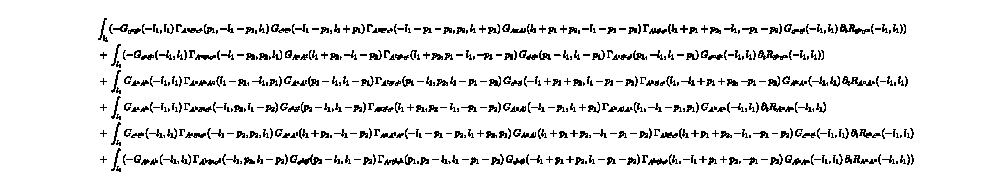

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZAcbc/ZAcbc.hh unchanged

Exported to "/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZAcbc/kernel.hh"

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZAcbc/src/constructor.cc unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZAcbc/src/CT_get.cc unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZAcbc/src/CT_map_1.cc unchanged

Please run UpdateFlows[] to export an up-to-date CMakeLists.txt

Exported to "/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/CMakeLists.txt"

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.hh unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.cc unchanged

```mathematica
fRGAcbc=TakeDerivatives[WetterichEquation,{A[i1],cb[i2],c[i3]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;

projectorAcbc=TBGetProjector["Acbc",1,{i1,i2,i3}/.fRGAcbc["1-Loop"]["ExternalIndices"]];
traceExprAcbc=F[projectorAcbc,(fRGAcbc["1-Loop"]["Expression"]/.MakeDiagrammaticRules[])];

FlowAcbc=FormTrace[traceExprAcbc,SP3FormRule,SP3FormRule]//dressingRules//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3]&//SPParam;

MakeKernel[FlowAcbc,kernelZAcbc,kernelParameterList,
"KernelBody"->SP3Defs,
"IntegrationVariables"->{"l1","cos1","cos2"},
"Coordinates"->{"LogarithmicCoordinates1D<double>"},
"CoordinateArguments"->{"p"}]
UpdateFlows["YangMillsFlows"]
```

## Three-Gluon Vertex

```mathematica
fRGA3=TakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP3]&//FPlot//FRoute//FPrint;

projectorA3=TBGetProjector["AAAClassTrans",1,{i1,i2,i3}/.fRGA3["1-Loop"]["ExternalIndices"]]//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3]&//Simplify;
traceExprA3=F[projectorA3,(fRGA3["1-Loop"]["Expression"]/.MakeDiagrammaticRules[])];
FlowA3=FormTrace[traceExprA3,{},SP3FormRule]//dressingRules//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3]&//SPParam;

MakeKernel[FlowA3,kernelZA3,kernelParameterList,
"KernelBody"->SP3Defs,
"IntegrationVariables"->{"l1","cos1","cos2"},
"Coordinates"->{"LogarithmicCoordinates1D<double>"},
"CoordinateArguments"->{"p"}]
UpdateFlows["YangMillsFlows"]
```

3 -Graphics--6 -Graphics--3 -Graphics-

-Graphics-

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA3/ZA3.hh unchanged

Exported to "/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA3/kernel.hh"

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA3/src/constructor.cc unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA3/src/CT_get.cc unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA3/src/CT_map_1.cc unchanged

Please run UpdateFlows[] to export an up-to-date CMakeLists.txt

Exported to "/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/CMakeLists.txt"

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.hh unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.cc unchanged

## Four-Gluon Vertex

3 -Graphics--12 -Graphics--6 -Graphics--24 -Graphics-+12 -Graphics-

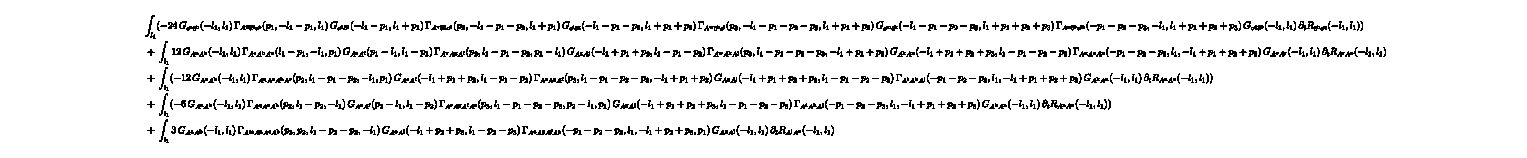

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA4/ZA4.hh unchanged

Exported to "/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA4/kernel.hh"

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA4/src/constructor.cc unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA4/src/CT_get.cc unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/ZA4/src/CT_map_1.cc unchanged

Please run UpdateFlows[] to export an up-to-date CMakeLists.txt

Exported to "/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/CMakeLists.txt"

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.hh unchanged

/home/franz/Documents/Uni/Code/DiFfRG/Examples/YangMills/SP/flows/flows.cc unchanged

```mathematica
fRGA4=TakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3],A[i4]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP4]&//FPlot//FRoute//FPrint;

projectorA4=TBGetProjector["AAAAClassTrans",1,{i1,i2,i3,i4}/.fRGA4["1-Loop"]["ExternalIndices"]]//Simplify;
traceExprA4=F[projectorA4,(fRGA4["1-Loop"]["Expression"]/.MakeDiagrammaticRules[])];
FlowA4=FormTrace[traceExprA4,SP4FormRule,SP4FormRule]//dressingRules//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3,p4]&//SPParam;

MakeKernel[Collect[FlowA4,{ZA3[__],ZA4[__],ZAcbc[__]},Simplify],kernelZA4,kernelParameterList,
"KernelBody"->SP4Defs,
"IntegrationVariables"->{"l1","cos1","cos2","phi"},
"Coordinates"->{"LogarithmicCoordinates1D<double>"},
"CoordinateArguments"->{"p"}]
UpdateFlows["YangMillsFlows"]
```